```mathematica
dat=Import[NotebookDirectory[]<>"toplot.dat"];
datn=Select[#,NumberQ]&/@Transpose@dat;Ordering[Length/@datn]
```

{16,10,18,9,14,12,5,2,4,20,19,15,1,7,13,8,11,6,3,17}

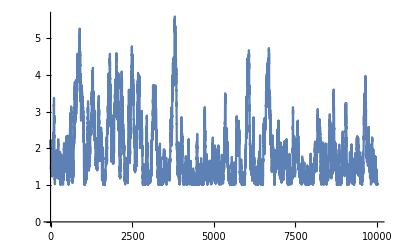

```mathematica
dat[[;;,17]]//ListLinePlot
```

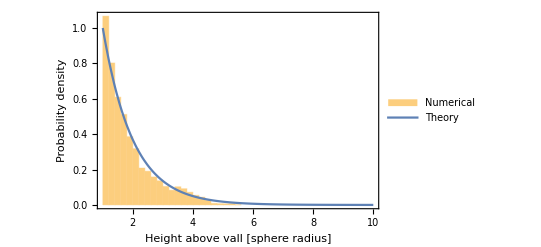

```mathematica
Show[
Histogram[
Select[dat[[;;,17]],#≠0&]
,{1,10,0.2},"PDF",ChartLegends->{"Numerical"}],
Plot[Exp[-(x-1)],{x,1,10},PlotRange->All,PlotLegends->{"Theory"}],
Frame->True,
FrameLabel-> {"Height above vall [sphere radius]","Probability density"}
]
```